### Conditional distribution of gene trees matching the species tree

Confirm that we have computed the joint probabilities correctly.

```mathematica
FullSimplify[
  (1-ⅇ^-d)(1-ⅇ^-c)+
(1-ⅇ^-d)(ⅇ^-c)2/3+
(1-ⅇ^-d)(ⅇ^-c)1/3+
(ⅇ^-d)(1-3/2 ⅇ^-c+1/2 ⅇ^(-3c))1/3+
(ⅇ^-d)(3/2 ⅇ^-c-3/2 ⅇ^(-3c))1/3*2/3+
(ⅇ^-d)(3/2 ⅇ^-c-3/2 ⅇ^(-3c))1/3*1/3+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/9+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/18]
```

1-(2 ⅇ^-d)/3

0

```mathematica
FullSimplify[
  Integrate[Exp[-x]Exp[-y],{x,0,d},{y,0,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-c)Integrate[Exp[-x]Exp[-3y]3*2/3,{x,0,d},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-c)Integrate[Exp[-x]Exp[-3y]3*1/3,{x,0,d},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]Exp[x-y]1/3,{x,0,c},{y,x,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))2/3,{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))1/3,{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/9+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/18]
```

1-(2 ⅇ^-d)/3

Now compute expected length

```mathematica
FullSimplify[
(Integrate[Exp[-x]Exp[-y]((d-x)Subscript[μ, 1]+y Subscript[μ, 2]),{x,0,d},{y,0,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+(ⅇ^-c)Integrate[Exp[-x]Exp[-3y]3*2/3*((d-x)Subscript[μ, 1]+c Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,d},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-c)Integrate[Exp[-x]Exp[-3y]3*1/3*((d-x)Subscript[μ, 1]+c Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,d},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3 Exp[-3x]Exp[x-y]1/3 (y-x)Subscript[μ, 2],{x,0,c},{y,x,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))2/3((c-x)Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))1/3((c-x)Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)(ⅇ^(-3c))1/18 *1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/9*(1/3+2)Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3])]
```

1/6 ⅇ^(-3 c-d) (μ_2-μ_3+ⅇ^(2 c) (6 ⅇ^c (1+(-1+d) ⅇ^d) μ_1+(3-4 ⅇ^c+6 ⅇ^d (-1+ⅇ^c)) μ_2+3 (-1+2 ⅇ^d) μ_3))

Add conditional part (division) and factorize by rates

```mathematica
FullSimplify[(1/6 ⅇ^(-3 c-d) (μ2-μ3+ⅇ^(2 c) (6 ⅇ^c (1+(-1+d) ⅇ^d) μ1+(3-4 ⅇ^c+6 ⅇ^d (-1+ⅇ^c)) μ2+3 (-1+2 ⅇ^d) μ3)))/(1-(2 ⅇ^-d)/3)-(ⅇ^-d/(3-2 ⅇ^-d) (3 μ1(1+(-1+d) ⅇ^d )+μ2/2(ⅇ^(-3 c)-3 ⅇ^(- c)(2 ⅇ^d -1)-4 +6 ⅇ^d )+  μ3/2(-ⅇ^(-3 c)+3 ⅇ^-c (2 ⅇ^d-1) ) ))]
```

0

### Conditional distribution of gene trees NOT matching the species tree

```mathematica
FullSimplify[
(ⅇ^-d)Integrate[3Exp[-3x]Exp[x-y]1/3,{x,0,c},{y,x,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))2/3,{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))1/3,{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/9+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/18+
(ⅇ^-d)(ⅇ^(-3c))1/18]
```

ⅇ^-d/3

```mathematica
FullSimplify[
(ⅇ^-d)Integrate[3 Exp[-3x]Exp[x-y]1/3 (y-x)Subscript[μ, 2],{x,0,c},{y,x,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))2/3((c-x)Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))1/3((c-x)Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)(ⅇ^(-3c))1/18 *1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/9*(1/3+2)Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]]
```

1/6 ⅇ^(-3 c-d) ((-1+ⅇ^c)^2 (1+2 ⅇ^c) μ_2+(-1+3 ⅇ^(2 c)) μ_3)

Add conditional part and factorize by rates

```mathematica
FullSimplify[1/6 ⅇ^(-3 c-d) ((-1+ⅇ^c)^2 (1+2 ⅇ^c) μ2+(-1+3 ⅇ^(2 c)) μ3)/(ⅇ^-d/3)-(μ2/2 (ⅇ^(-3 c)-3 ⅇ^-c+2) +μ3/2 (-ⅇ^(-3 c) +3 ⅇ^-c) )]
```

0

### Limits and testing

```mathematica
eL[d_,c_,μ1_,μ2_,μ3_]:=ⅇ^-d/(3-2 ⅇ^-d) (3 μ1(1+(-1+d) ⅇ^d)+μ2/2(ⅇ^(-3 c)-3 ⅇ^(- c)(2 ⅇ^d-1)-4 +6 ⅇ^d )+μ3/2(-ⅇ^(-3 c)+3 ⅇ^-c (2 ⅇ^d-1) ))
eA[d_,c_,μ1_,μ2_,μ3_]:=μ2/2 (ⅇ^(-3 c)-3 ⅇ^-c+2) +μ3/2(-ⅇ^(-3 c) +3 ⅇ^-c) 
eLap[d_,μ1_,μ2_]:=(3 (1+(-1+d) ⅇ^d) μ1)/(-2+3 ⅇ^d)+μ2
eAap[d_,μ1_,μ2_]:=μ2
```

```mathematica
FullSimplify[eL[d,c,μ1,μ2,μ3]-eA[d,c,μ1,μ2,μ3]]
```

(3 ⅇ^(-3 c) (μ2-μ3+ⅇ^(2 c) (2 ⅇ^c μ1-μ2+μ3)+ⅇ^d (-μ2+ⅇ^(2 c) (2 (-1+d) ⅇ^c μ1+μ2-μ3)+μ3)))/(2 (-2+3 ⅇ^d))

```mathematica
{FullSimplify[eL[d,c,μ1,μ2,μ2]],FullSimplify[eA[d,c,μ1,μ2,μ2]]}
{FullSimplify[eL[d,c,μ1,μ1,μ1]],FullSimplify[eA[d,c,μ1,μ1,μ1]]}
```

{(3 (1+(-1+d) ⅇ^d) μ1)/(-2+3 ⅇ^d)+μ2,μ2}

{((1+3 d ⅇ^d) μ1)/(-2+3 ⅇ^d),μ1}

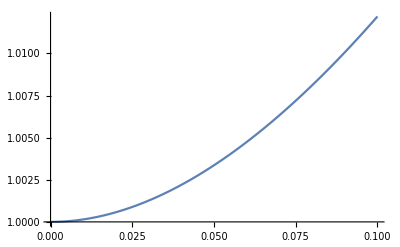

0.710504

```mathematica
Plot[{(1+3 d ⅇ^d)/(-2+3 ⅇ^d)},{d,0,0.1}]
eL[10,10,0.00001,0.01,1000]/eA[10,10,0.00001,0.01,1000]
```

```mathematica
FullSimplify[eL[d,c,μ1,μ2,μ2]-eA[d,c,μ1,μ2,μ2]]
FullSimplify[eL[d,c,μ1,μ1,μ1]-eA[d,c,μ1,μ1,μ1]]
```

(3 (1+(-1+d) ⅇ^d) μ1)/(-2+3 ⅇ^d)

(3 (1+(-1+d) ⅇ^d) μ1)/(-2+3 ⅇ^d)

```mathematica
FullSimplify[Limit[eL[d,c,μ1,μ2,μ3],c->Infinity]]
FullSimplify[Limit[eA[d,c,μ1,μ2,μ3],c->Infinity]]
```

(3 (1+(-1+d) ⅇ^d) μ1)/(-2+3 ⅇ^d)+μ2

μ2

### Testing

Test for replicates 2, 3, and 5 with high hg, hl, hs (qt)

```mathematica
{df,cf,μ1f,μ2f,μ3f,μf,popf} = {2.4611402928,0.8683444694,0.03316616,0.27338745,1.51208253,9.962003*10^-5,100}
eL[df,cf,μ1f,μ2f,μ3f]*μf*popf
eLap[df,μ1f,μ2f]*μf*popf
eA[df,cf,μ1f,μ2f,μ3f]*μf*popf
eAap[df,μ1f,μ2f]*μf*popf
{df,cf,μ1f,μ2f,μ3f,μf,popf} = {0.0123537981,0.9406345232,0.70698324,1.23060446,0.52242135,1.018401*10^-4,100}
eL[df,cf,μ1f,μ2f,μ3f]*μf*popf
eLap[df,μ1f,μ2f]*μf*popf
eA[df,cf,μ1f,μ2f,μ3f]*μf*popf
eAap[df,μ1f,μ2f]*μf*popf
{df,cf,μ1f,μ2f,μ3f,μf,popf} = {0.4840481216,3.1786325017,0.76585139,1.34358175,0.85401910,2.388133*10^-4,100}
eL[df,cf,μ1f,μ2f,μ3f]*μf*popf
eLap[df,μ1f,μ2f]*μf*popf
eA[df,cf,μ1f,μ2f,μ3f]*μf*popf
eAap[df,μ1f,μ2f]*μf*popf
```

{2.46114,0.868344,0.0331662,0.273387,1.51208,0.00009962,100}

0.00850799

0.00326527

0.0100351

0.00272349

{0.0123538,0.940635,0.706983,1.2306,0.522421,0.00010184,100}

0.00856831

0.0125341

0.00852381

0.0125325

{0.484048,3.17863,0.765851,1.34358,0.854019,0.000238813,100}

0.0346296

0.0352012

0.0313567

0.0320865

Test for replicates 4, 8, and 1, 10 with low hg, hl, and high hs (qtonlyhg)

```mathematica
{df,cf,μ1f,μ2f,μ3f,μf,popf} = {0.4781149352,3.3430932007,1.10354197,0.95885629,1.03219992,2.508077*10^-4,100}
eL[df,cf,μ1f,μ2f,μ3f]*μf*popf
eLap[df,μ1f,μ2f]*μf*popf
eA[df,cf,μ1f,μ2f,μ3f]*μf*popf
eAap[df,μ1f,μ2f]*μf*popf
{df,cf,μ1f,μ2f,μ3f,μf,popf} = {0.2416848997,2.5034378178,0.71318340,1.46265681,0.48974104,3.841142*10^-4,100}
eL[df,cf,μ1f,μ2f,μ3f]*μf*popf
eLap[df,μ1f,μ2f]*μf*popf
eA[df,cf,μ1f,μ2f,μ3f]*μf*popf
eAap[df,μ1f,μ2f]*μf*popf
{df,cf,μ1f,μ2f,μ3f,μf,popf} = {1.3545904293,2.2304662810,0.17959308,2.20288049,0.53224105, 4.083158*10^-4,100}
eL[df,cf,μ1f,μ2f,μ3f]*μf*popf
eLap[df,μ1f,μ2f]*μf*popf
eA[df,cf,μ1f,μ2f,μ3f]*μf*popf
eAap[df,μ1f,μ2f]*μf*popf
```

{0.478115,3.34309,1.10354,0.958856,1.0322,0.000250808,100}

0.0287516

0.0286751

0.0241463

0.0240489

{0.241685,2.50344,0.713183,1.46266,0.489741,0.000384114,100}

0.0538432

0.0577344

0.0516073

0.0561827

{1.35459,2.23047,0.179593,2.20288,0.532241,0.000408316,100}

0.0876651

0.0953731

0.078992

0.0899471

### Checking against Rosenberg, 2002

```mathematica
Pt1[d_,c_]:=  (1-ⅇ^-d)(1-ⅇ^-c)+(1-ⅇ^-d)(ⅇ^-c)1/3+(ⅇ^-d)(1-3/2 ⅇ^-c+1/2 ⅇ^(-3c))1/3+(ⅇ^-d)(3/2 ⅇ^-c-3/2 ⅇ^(-3c))1/3*1/3+(ⅇ^-d)(ⅇ^(-3c))*1/18

g11[T_]:=1
g21[T_]:=1−ⅇ^(−T)
g22[T_]:=ⅇ^(−T)
g31[T_]:=1−3/2 ⅇ^(−T)+1/2 ⅇ^(−3T)
g32[T_]:=3/2 ⅇ^(−T)−3/2 ⅇ^(−3T) 
g33[T_]:=ⅇ^(−3T)
Pt1R[T3_,T2_]:=g21[T3](g21[T2]+g22[T2] 1/3)+g22[T3](g31[T2] 1/3+g32[T2] 1/3 1/3+g33[T2] 1/3 1/6)

{df,cf,μ1f,μ2f,μ3f,μf,popf} = {2.45924,0.868,0.03316616,0.27338745,1.51208253,9.962003*10^-5,100}
Pt1[df,cf]*10000
Pt1R[df,cf]*10000
{df,cf,μ1f,μ2f,μ3f,μf,popf} = {0.0123537981,0.9406345232,0.70698324,1.23060446,0.52242135,1.018401*10^-4,100}
Pt1[df,cf]*10000
Pt1R[df,cf]*10000
```

{2.45924,0.868,0.0331662,0.273387,1.51208,0.00009962,100}

6754.55

6754.55

{0.0123538,0.940635,0.706983,1.2306,0.522421,0.00010184,100}

2130.59

2130.59

```mathematica
df
```

0.0123538

```mathematica
(ⅇ^-d)(1-3/2 ⅇ^-c+1/2 ⅇ^(-3c))1/3+
```

```mathematica
FullSimplify[(1-ⅇ^-d)(1-ⅇ^-c)+(1-ⅇ^-d)(ⅇ^-c)1/3+(ⅇ^-d)(1-3/2 ⅇ^-c+1/2 ⅇ^(-3c))1/3+(ⅇ^-d)(3/2 ⅇ^-c-3/2 ⅇ^(-3c))1/3*1/3+(ⅇ^-d)(ⅇ^(-3c))*1/18]
```

1/18 ⅇ^(-3 c-d) (1+6 ⅇ^(2 c) (1-2 ⅇ^c+ⅇ^d (-2+3 ⅇ^c)))

### Mean branch length conditioned on species tree matching the gene tree (WRONG!)

```mathematica
FullSimplify[Integrate[Exp[-x]Exp[d-y],{x,0,d},{y,d,d+c},Assumptions->d∈PositiveReals&&c∈PositiveReals ]+
Integrate[Exp[-x]Exp[d-y],{x,0,d},{y,d+c,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+Integrate[Exp[-x]Exp[x-y],{x,d,d+c},{y,x,d+c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
Integrate[Exp[-x]Exp[x-y],{x,d,d+c},{y,d+c,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
Integrate[Exp[-x]Exp[x-y],{x,d+c,Infinity},{y,x,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals],Assumptions->d∈PositiveReals&&c∈PositiveReals]
```

1

```mathematica
FullSimplify[Integrate[Exp[-x]Exp[d-y](Subscript[μ, 1](d-x)+Subscript[μ, 2](y-d)),{x,0,d},{y,d,d+c},Assumptions->d∈PositiveReals&&c∈PositiveReals ]+
Integrate[Exp[-x]Exp[d-y](Subscript[μ, 1](d-x)+Subscript[μ, 2] c+Subscript[μ, 3](y-d-c)),{x,0,d},{y,d+c,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+Integrate[Exp[-x]Exp[x-y] Subscript[μ, 2](y-x),{x,d,d+c},{y,x,d+c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
Integrate[Exp[-x]Exp[x-y](Subscript[μ, 2](d+c-x)+Subscript[μ, 3](y-d-c)),{x,d,d+c},{y,d+c,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
Integrate[Exp[-x]Exp[x-y] Subscript[μ, 3](y-x),{x,d+c,Infinity},{y,x,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]]
```

ⅇ^(-c-d) (ⅇ^c (1+(-1+d) ⅇ^d) μ_1+(-c+ⅇ^d (-1+ⅇ^c)) μ_2+(c+ⅇ^d) μ_3)

### Conditional distribution of gene trees matching the species tree (rooted case)

Compute expected length with the “other side” branch

```mathematica
FullSimplify[
(Integrate[Exp[-x]Exp[-y]((d-x)Subscript[μ, 1]+y Subscript[μ, 2]),{x,0,d},{y,0,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+(ⅇ^-c)Integrate[Exp[-x]Exp[-3y]3*2/3*((d-x)Subscript[μ, 1]+c Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,d},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-c)Integrate[Exp[-x]Exp[-3y]3*1/3*((d-x)Subscript[μ, 1]+c Subscript[μ, 2]+(y+1) Subscript[μ, 3]),{x,0,d},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3 Exp[-3x]Exp[x-y]1/3 (y-x)Subscript[μ, 2],{x,0,c},{y,x,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))2/3((c-x)Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))1/3((c-x)Subscript[μ, 2]+(y+1) Subscript[μ, 3]),{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)(ⅇ^(-3c))1/18 *1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/9*(1/3+1)Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3])]
```

1/18 ⅇ^(-3 c-d) (3 μ_2-2 μ_3+3 ⅇ^(2 c) (6 ⅇ^c (1+(-1+d) ⅇ^d) μ_1+(3-4 ⅇ^c+6 ⅇ^d (-1+ⅇ^c)) μ_2+2 (-1+2 ⅇ^d) μ_3))

Add conditional part (division) and factorize by rates

```mathematica
FullSimplify[(1/18 ⅇ^(-3 c-d) (3 μ2-2 μ3+3 ⅇ^(2 c) (6 ⅇ^c (1+(-1+d) ⅇ^d) μ1+(3-4 ⅇ^c+6 ⅇ^d (-1+ⅇ^c)) μ2+2 (-1+2 ⅇ^d) μ3)))/(1-(2 ⅇ^-d)/3)-(ⅇ^-d/(3-2 ⅇ^-d) (3 μ1(1+(-1+d) ⅇ^d )+μ2/2(ⅇ^(-3 c)-3 ⅇ^(- c)(2 ⅇ^d -1)-4 +6 ⅇ^d )+  μ3/3(-ⅇ^(-3 c)+3 ⅇ^-c (2 ⅇ^d-1) ) ))]
```

0

```mathematica
FullSimplify[
(ⅇ^-d)Integrate[3 Exp[-3x]Exp[x-y]1/3 (y-x)Subscript[μ, 2],{x,0,c},{y,x,c},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))2/3((c-x)Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(c-x)))1/3((c-x)Subscript[μ, 2]+(y+1) Subscript[μ, 3]),{x,0,c},{y,0,Infinity},Assumptions->d∈PositiveReals&&c∈PositiveReals]+
(ⅇ^-d)(ⅇ^(-3c))1/18 *1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/9*(1/3+1)Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]+
(ⅇ^-d)(ⅇ^(-3c))1/18*1/3 Subscript[μ, 3]]
```

1/18 ⅇ^(-3 c-d) (3 (-1+ⅇ^c)^2 (1+2 ⅇ^c) μ_2+2 (-1+3 ⅇ^(2 c)) μ_3)

Add conditional part and factorize by rates

```mathematica
FullSimplify[(1/18 ⅇ^(-3 c-d) (3 (-1+ⅇ^c)^2 (1+2 ⅇ^c) μ2+2 (-1+3 ⅇ^(2 c)) μ3))/(ⅇ^-d/3)-(μ2/2 (ⅇ^(-3 c)-3 ⅇ^-c+2) +μ3/3 (-ⅇ^(-3 c) +3 ⅇ^-c) )]
```

0

```mathematica
Integrate[x Exp[-x],{x,0,c}]
```

1-(1+c) ⅇ^-c